# Implementing REigs from Jia et al

Pseudocode is on p11 of https://arxiv.org/ftp/arxiv/papers/2102/2102.09693.pdf
There are some typos.  I am doing this in a script first

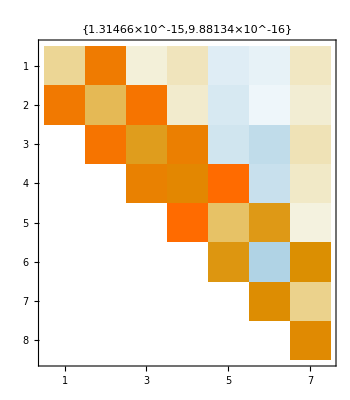

```mathematica
m=23;
d=RandomReal[{1,10},m];
od=0.1 RandomReal[{-1,1},m-1];
B= SparseArray[{
Band[{1,2}]->od,
Band[{2,1}]->od,
Band[{1,1}]->d},{m,m}];
(*B=IdentityMatrix[m];*)
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
(* Step 1 build v *)
v=RandomReal[{-1,1},m];
v=v/(√(v.B.v));
v0=v;
(* Step 2 and 3 Arnoldi *)
{k,p}={4,3};
k+p+1 ≤ m;
V=ConstantArray[0,{m,k+p+1}];
HBig=ConstantArray[0,{k+p+1,k+p}];
V⟦All,1⟧=v;
Do[
v=LinearSolve[B,A.v];
Do[
HBig⟦j,n⟧=V⟦All,j⟧.B.v;
v=v-HBig⟦j,n⟧ V⟦All,j⟧,
{j,1,n}];
HBig⟦n+1,n⟧=√(v.B.v);
v=v/HBig⟦n+1,n⟧;
V⟦All,n+1⟧=v,
{n,1,k+p}];
MatrixPlot[HBig,PlotLabel->Map[Norm,
{Vᵀ.B.V-IdentityMatrix[k+p+1],A.V⟦All,1;;k+p⟧-B.V.HBig}]]
```

```mathematica
(* Compute and sort the eigenvalues of the inner matrix *)
H=HBig⟦1;;k+p⟧;
λs=Sort[Eigenvalues[H]];
σs=λs⟦1;;p⟧;
(*{λs,Qs}=Sort[Eigensystem[Chop[H⟦1;;k+p⟧]]ᵀ]ᵀ; *)
Id=IdentityMatrix[k+p];
Q=Id;
Do[
{Qj,Rj}=QRDecomposition[H-σs⟦j⟧ Id];Qj=Qjᵀ;
H=ConjugateTranspose[Qj].H.Qj;
Q=Q.Qj,
{j,1,p}]
(* Throw away stuff from V and H *)
H=H⟦1;;k,1;;k⟧;
V =V⟦All,1;;k+p⟧.Q⟦All,1;;k⟧;
```